```mathematica
Remove["Global`*"];
U:=Random[];
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

### Cholera Epidemic Simulation Xinyu Ma, Thanh Tran, Ngoc Tran

```mathematica
ω=0.00192;  (* immunity waning rate, units=1/day *)
p=0.98;  (* fraction of asymptomatic infecteds *)
η1=0.5;  (* asymptomatic shedding rate, units= 1/day *)
η2=50.0;  (* symptomatic shedding rate, units= 1/day *)
γ1=0.15;  (* asymptomatic recovery rate, units=1/day *)
γ2=0.031;  (* asymptomatic recovery rate, units=1/day *)
χ=5.0;  (* bacteria transition rate, units=1/day *)
δ=0.0333;  (* bacteria death rate, units=1/day*)
e1=0.0;  (* asymptomatic death rate, units=1/day *)
e2=0.01277;  (* symptomatic death rate, units=1/day *)
βL=0.214;  (* less-infectious ingestion rate, units=1/day *)
βH=0.214;  (* hyperinfectious ingestion rate, units=1/day *)
κL = 10^6;    (* half saturation constant - less infectious *)
κH = 10^6/700; (* half saturation constant - hyperinfectious *)
v = 0; (* v is the fraction of the 10% maximum vaccination rate *)
q = 0; (* q is the quarantine fraction *)
```

```mathematica
day:=Module[{},

(* compute changes in population values based on transition rates *)
dS=0;dIa=0;dIs=0;dR=0;
dBL=0;  (* <---- NOTE: PLEASE ADD THIS LINE *)

(* If the population is vaccinated *)
Do[If[U<v/10,dS--;dR++,
(* if the population is not *)
If[U< ((βL BL)/(κL +BL) + (βH BH)/(κH +BH)),dS--;If[U<p,dIa++,dIs++]]],{S}];  (* S -> Ia || Is *)     
Do[If[U<γ1,dIa--;dR++],{Ia}];  (* Ia -> R *) 
Do[If[U<γ2,dIs--;dR++],{Is}];  (* Is -> R *) 
Do[If[U<e2,dIs--],{Is}];  (* Is -> death *) 
Do[If[U<ω,dR--;dS++],{R}];  (* R -> S *)
Do[If[U<δ,dBL-=200],{BL/200}];  (* BL -> death (in groups of 200 for efficiency)*) 
 
BL=BL+dBL;  (* <---- NOTE: PLEASE ADD THIS LINE *)

(* Run on a one hour time scale for bacteria *)
Do[
dBH=0;dBL=0;
Do[If[U<η1/24,dBH++],{Ia}];  (* BH from Ia *) 
Do[If[U<(1-q) η2/240,dBH+=10],{Is}];  (* BH from Is *) 
Do[If[U<χ/24,dBH--;dBL++],{BH}]; (* BH -> BL *) 
BH=BH+dBH;
BL=BL+dBL,
{24}];

(* update population values each day*)
S=S+dS;
Ia=Ia+dIa;
Is=Is+dIs;
R=R+dR;

n=S+Ia+Is+R;
t++;

(* update daily lists *)
AppendTo[tList,t];
AppendTo[nList,n];
AppendTo[SList,S];
AppendTo[IaList,Ia];
AppendTo[IsList,Is];
AppendTo[RList,R];
AppendTo[BHList,BH];
AppendTo[BLList,BL];

]
```

```mathematica
infect[numDays_]:=Module[{},

(* initialize population values *)
S=9900;  
Ia=98;   
Is=2;  
R=0;   
totalPeople=S+Ia+Is+R;
BH=0;   
BL=0;
n=S+Ia+Is+R;
t=0;

(* initialize daily lists *)
SList={S};  
IaList={Ia};
IsList={Is};
RList={R};
BHList={BH};
BLList={BL};
tList={0};
nList={n};

Do[day,{numDays}];
plot1=ListPlot[{SList,IaList,IsList,RList,nList},Joined->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],AspectRatio->0.5,PlotStyle->Thick,Frame->True,PlotLegends->{"S","Ia","Is","R","n"}];
plot2=ListPlot[{BHList,BLList},Joined->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],AspectRatio->0.5,PlotStyle->Thick,Frame->True,PlotLegends->{"BH","BL"}];

Return[{plot1,plot2,totalPeople-n}];
]
```

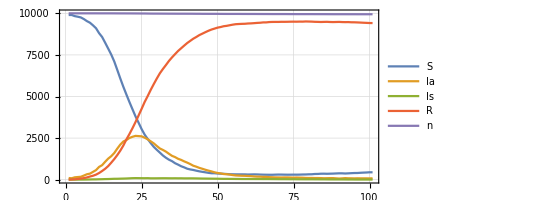

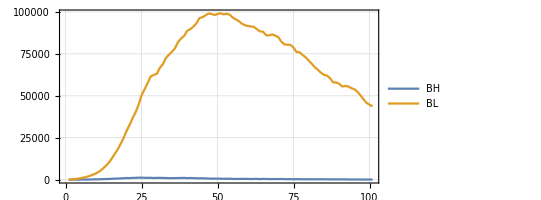

55

```mathematica
popData=infect[100];
popData[[1]]
popData[[2]]
popData[[3]]
```

```mathematica
improvCholera[vac_,quar_]:=Module[{},
v=(vac-1)/10;
q=(quar-1)/10;
data={infect[100][[3]]};
proc--;
For[i=1,i<20,i++,AppendTo[data,infect[100][[3]]];proc--];
mean= Mean[data]//N;
std=StandardDeviation[data];
ci95=(1.96*std)/(20)^0.5;
Return[{mean,ci95}];
]
```

```mathematica
proc=11*20;
Monitor[deathTable=Array[improvCholera,{1,11},{11,1}],proc]
```

{{{4.15,1.08548},{4.35,1.25803},{4.6,1.45288},{3.,0.887997},{2.4,0.702383},{2.4,0.770997},{1.6,0.575839},{1.2,0.504736},{1.8,0.524383},{1.05,0.502226},{1.15,0.356194}}}